## This notebook calculates transition path times in a 2D Langevin system as in “Medina, E., Satija, R., & Makarov, D. E. (2018). Transition path times in non-Markovian activated rate processes. The Journal of Physical Chemistry B, 122(49), 11400-11413.”

### 1. In this section, we solve Langevin equations numerically and collect transition paths from long trajectories.

```mathematica
temp = 1(* temperature sets the energy scale *)
```

```mathematica
gamX = 1.0 (* friction coefficient along X, without loss of generality can be set to 1. This sets the time scale, since in the overdamped limit the time enters equations of motion in dimensionless combination of (time/friction coefficient)  *)
```

```mathematica
gamY=10.0 (* friction coefficient along Y, calculated in units of gamX *)
```

```mathematica
x0  = -0.57735(* Left transition boundary; unit of length taken as 1 *)
```

```mathematica
x1 = -x0 (* Right transition boundary *)
```

2D potential (parabolic barrier + harmonic oscillator + linear coupling)

```mathematica
V0 = 1 (* barrier height *)
```

```mathematica
k = 8  (* curvature along y at the transition state  *)
```

```mathematica
Clear[pot1D, x, y]; pot1D[x_] =V0*(x^2-1)^2
```

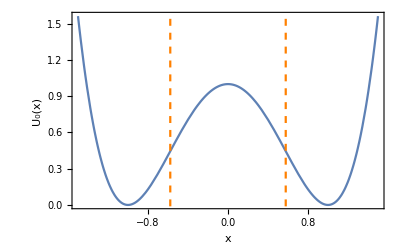

```mathematica
plx0 = ParametricPlot[{x0, y}, {y, -10, 10},  PlotStyle->Directive[Orange,Dashed]];
plx1 = ParametricPlot[{x1, y}, {y, -10, 10},  PlotStyle->Directive[Orange,Dashed]];
plFE1D = Show[Plot[pot1D[x], {x, -1.5, 1.5}], plx0, plx1, Axes->False,LabelStyle -> Directive[10], Frame->{{True, True}, {True, True}}, FrameLabel->{{Style["U_0(x)",10,Black], ""}, {Style["x",10,Black], Style["  x_a                                  x_b",10,Black]}}]
```

```mathematica
Export["FigS3b.pdf", plFE1D]
```

(-1+x^2)^2+4 (-x+y)^2

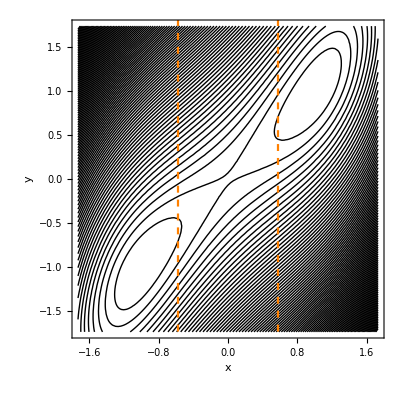

```mathematica
Clear[pot, x,y]; pot[x_,y_] = pot1D[x] + (1/2) k (y-x)^2
plx0 = ParametricPlot[{x0, y}, {y, -10, 10},  PlotStyle->Directive[Orange,Dashed]];
plx1 = ParametricPlot[{x1, y}, {y, -10, 10},  PlotStyle->Directive[Orange,Dashed]];
plCon = Show[ContourPlot[pot[x,y], {x, -3x0,3 x0}, {y, -3x0,3x0}, Contours -> 100, ContourShading->None, FrameLabel -> {{Style["y",15,Black],""},{Style["x",15,Black],Style["x_a                   x_b",15,Black]}}, LabelStyle -> Directive[15]],plx0,plx1]
```

```mathematica
Export["FigS3a.pdf", plCon]
```

```mathematica
Clear[force,x,y]; force[x_,y_] = -{D[pot[x,y], x], D[pot[x,y], y]}
```

```mathematica
Clear[freeEn, x]; (* free energy *) freeEn[x_] = pot1D[x]
```

This function generates a random variable with a normal distribution:

```mathematica
Clear[gaussianRandom]; gaussianRandom := Module[{x,y}, x = Random[Real, {0, 1}]; y = Random[Real, {0, 1}]; Sqrt[-2 Log[x]] Cos[2 Pi y]]
```

This is a single time step in the stochastic dynamics algorithm a la Schulten:

```mathematica
Clear[move]; move[{t_, x_,y_}, dt_] := Module[{r1,r2, tN, xN, yN}, r1 = gaussianRandom;r2=gaussianRandom; tN = t + dt; xN = x + force[x,y][[1]] dt/gamX + Sqrt[2 dt temp/ gamX] r1; yN = y + force[x,y][[2]] dt/gamY + Sqrt[2 dt temp/ gamY] r2;{tN, xN,yN}]
```

```mathematica
move[{0, 0.1,0.1}, 0.01]
```

```mathematica
dt = 0.0005  (* time step to be used *)
```

Example of generating a trajectory

```mathematica
tMax = 10000.0
```

```mathematica
ll= Floor[tMax/dt]+1
trajectory=NestList[move[#,dt]&, {0,0,0},ll];
```

Code to extract transition paths:

```mathematica
rA=x0; rB=x1;
traj=Map[#[[2]]&, trajectory];
splittraj=SplitBy[traj,((#>rA)&&(#<rB))&];
tpaths=Select[Table[If[(Last[splittraj[[i-1]]]<rA&&First[splittraj[[i+1]]]>rB)||(Last[splittraj[[i-1]]]>rB&&First[splittraj[[i+1]]]<rA),splittraj[[i]],Nothing],{i,2,Length@splittraj-1}],(rA<#[[1]]<rB)&];
tpt=(Length@#)*dt&/@tpaths;
```

Plot transition path times and calculate coefficient of variation:

```mathematica
pltpt = Histogram[tpt,200,"ProbabilityDensity", PlotRange->All, AxesLabel->{"t", "p_TP(t)"}]
pltpt = Histogram[tpt,20,"ProbabilityDensity", ScalingFunctions->"Log", PlotRange->All, AxesLabel->{"t", "p_TP(t)"}]
tMean =Mean[tpt]
tStd = (Mean[tpt^2]-tMean^2)^(1/2)
cv = tStd/tMean
```

### 2. Alternatively, for high enough barriers, we can apply the GSE approximation (Eq. 20-21 in reference cited in the title) to compute transition path time distribution analytically.

```mathematica
Clear[χ,t,γx,k,γy,k0]; χ[t_,γx_,k_,γy_,k0_]=(Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0]-(γx*k+γy*k+γy*k0))/(2Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0])Exp[-(Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0]+(γx*k+γy*k-γy*k0))/(2*γx*γy)t]+(Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0]+(γx*k+γy*k+γy*k0))/(2Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0])Exp[-((γx*k+γy*k-γy*k0)-Sqrt[(γx*k+γy*k-γy*k0)^2+4*γx*γy*k*k0])/(2*γx*γy)t];
pTP[t_,γx_,k_,γy_,k0_,dG_]=Sqrt[4/π*dG] D[χ[t,γx,k,γy,k0],t]/(Sqrt[χ[t,γx,k,γy,k0]^2-1]*(χ[t,γx,k,γy,k0]-1)*Erfc[Sqrt[dG]])Exp[-dG((χ[t,γx,k,γy,k0]+1)/(χ[t,γx,k,γy,k0]-1))] ;
Plot[pTP[t,1,1,10,4, 6.66], {t, 0, 5}]
norm=NIntegrate[pTP[t,1,1,10,4, 6.66], {t, 0.01, 100}]
meantpt=NIntegrate[t*pTP[t,1,1,10,4, 6.66], {t, 0.01, 100}]/norm
meantpt2=NIntegrate[t^2*pTP[t,1,1,10,4, 6.66], {t, 0.01, 100}]/norm
cvtpt = Sqrt[(meantpt2-meantpt^2)/meantpt^2]//Simplify
```

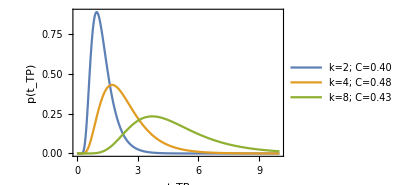

```mathematica
sizefont=15;
pl1=Plot[{pTP[t,1,2,10,4, 6.66], pTP[t,1,4,10,4, 6.66], pTP[t,1,8,10,4, 6.66]}, {t, 0., 10}, PlotRange->All, PlotLegends->Placed[{"k=2; C=0.40", "k=4; C=0.48", "k=8; C=0.43"}, {Right, Top}], Frame->{{True, False}, {True, False}},FrameLabel-> {{Style["p(t_TP)", Black,sizefont], Style["", Black,sizefont]}, {Style["t_TP", Black, sizefont], Style["", Black,sizefont]}}, FrameTicksStyle->Directive[Black, FontSize->sizefont],(* FrameStyle->Thick,*) ImageSize->300]
```

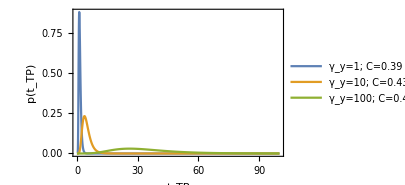

```mathematica
pl2=Plot[{pTP[t,1,8,1,4, 6.66], pTP[t,1,8,10,4, 6.66], pTP[t,1,8,100,4, 6.66]}, {t, 0, 100}, PlotRange->All, PlotLegends->Placed[{"γ_y=1; C=0.39", "γ_y=10; C=0.43", "γ_y=100; C=0.47"}, {Right, Top}], Frame->{{True, False}, {True, False}},FrameLabel-> {{Style["p(t_TP)", Black,sizefont], Style["", Black,sizefont]}, {Style["t_TP", Black, sizefont], Style["", Black,sizefont]}}, FrameTicksStyle->Directive[Black, FontSize->sizefont], (*FrameStyle->Thick,*) ImageSize->300]
```

```mathematica
Export["FigS4a.pdf", pl1]
```

```mathematica
Export["FigS4b.pdf", pl2]
```